```mathematica
Quit[]
```

```mathematica
ρ[t_]:=Table[a[i,j][t],{i,4},{j,4}]
slnn=Flatten[Table[a[i,j][t],{i,4},{j,4}]];
(*basis:a1a2,a1b2,b1a2,b1b2*)
inity=({{1, -I, -I, -1}, {I, 1, 1, -I}, {I, 1, 1, -I}, {-1, I, I, 1}})/4(*(e1-ig1)(e2-ig2)*);initx=1/4ConstantArray[1,{4,4}];(*(e1+g1)(e2+g2)*)
init=({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})(*e1g2*);
init1=({{0, 0, 0, 0}, {0, 1, 0, 1}, {0, 0, 0, 0}, {0, 1, 0, 1}})/2;initi=({{0, 0, 0, 0}, {0, 1, 0, I}, {0, 0, 0, 0}, {0, -I, 0, 1}})/2;(*(e1-ig1)g2*)
init1e=({{1, 0, 1, 0}, {0, 0, 0, 0}, {1, 0, 1, 0}, {0, 0, 0, 0}})/2;initie=({{1, 0, I, 0}, {0, 0, 0, 0}, {-I, 0, 1, 0}, {0, 0, 0, 0}})/2;(*(e1-ig1)e2*)
initetg=({{1, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 0, 1}})/2;(*e1e2+g1g2*)initetg2=({{0, 0, 0, 0}, {0, 1, 1, 0}, {0, 1, 1, 0}, {0, 0, 0, 0}})/2;
initth=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})/4;(*e1g2+g1e2*)r[i_,j_]:=(i-j)di;λ0=1;k0=2Pi/λ0;
x=0.05;
di=x λ0;
σ1p=({{0, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});σ1m=({{0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}});σ2p=({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}});σ2m=({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}});
γ=1(*ω0^3 μ^2/(3 Pi 8.85*10^-12*1.05*10^-34 c^3)*);θ=Pi/2;
F[k_]:=3/2((1-Cos[θ]^2)Sin[k di]/(k di)+(1-3 Cos[θ]^2)(Cos[k di]/(k di)^2-Sin[k di]/(k di)^3));
G[k_,R_]:=3/2((1-Cos[θ]^2)Sin[k R]/(k R)+(1-3 Cos[θ]^2)(Cos[k R]/(k R)^2-Sin[k R]/(k R)^3));
(*Λp[i_,j_]:=γ/(2Pi ω0^3)Integrate[ω^3 F[ω,i,j]/(ω-ω0),{ω,-10^30,10^30},PrincipalValue->True]*)
Λ12=3/4 γ(-(1-Cos[θ]^2)Cos[k0 di]/(k0 di)+(1-3 Cos[θ]^2)(Sin[k0 di]/(k0 di)^2+Cos[k0 di]/(k0 di)^3));
Λ21=3/4 γ(-(1-Cos[θ]^2)Cos[k0 di]/(k0 di)+(1-3 Cos[θ]^2)(Sin[k0 di]/(k0 di)^2+Cos[k0 di]/(k0 di)^3));
rr=0.5;
sh=Sinh[rr];
ch=Cosh[rr];
γ12=F[k0];
R=100Pi/k0;
(*Λp21=1/(2 Pi ω0^3)Exp[2I k0 (R)]NIntegrate[(x^2 √(x(2ω0-x)))/(-ω0+x)F[x-ω0,1,0],{x,0,2ω0},AccuracyGoal->30,Method->PrincipalValue,Exclusions->ω0,WorkingPrecision->40];Λp12=1/(2 Pi ω0^3)Exp[2I k0 (R)]NIntegrate[(x^2 √(x(2ω0-x)))/(-ω0+x)F[x-ω0,1,0],{x,0,2ω0},AccuracyGoal->30,Method->PrincipalValue,Exclusions->ω0,WorkingPrecision->40];
Λp11=1/(2 Pi ω0^3)Exp[2I k0 (R)]F[ω0,1,0]NIntegrate[(x^2 √(x(2ω0-x)))/(-ω0+x),{x,0,2ω0},Method->PrincipalValue,Exclusions->ω0,WorkingPrecision->40];
Λp22=1/(2 Pi ω0^3)Exp[2I k0 (R)]F[ω0,1,0]NIntegrate[(x^2 √(x(2ω0-x)))/(-ω0+x),{x,0,2ω0},Method->PrincipalValue,Exclusions->ω0,WorkingPrecision->40];*)
Λp21=Λp12=Λp11=Λp22=0;
γp12=Exp[I k0 2R];
γp21=Exp[I k0 2R];
γp11=γ12 Exp[I k0 2(R)];
γp22=γ12 Exp[I k0 2(R)];
```

```mathematica
(*4 sln to 4 init*)
SQ=-sh ch(((1/2γp21+I Λp21)( σ2p.σ1p.ρ[t]+ ρ[t].σ2p.σ1p)+(1/2γp12+I Λp12)( σ1p.σ2p.ρ[t]+ ρ[t].σ1p.σ2p))+((1/2γp21-I Λp21)( σ2m.σ1m.ρ[t]+ ρ[t].σ2m.σ1m)+(1/2γp12-I Λp12)( σ1m.σ2m.ρ[t]+ ρ[t].σ1m.σ2m))-((1γp21+2I Λp21) σ2p.ρ[t].σ1p+(1γp12+2I Λp12) σ1p.ρ[t].σ2p+(γp11+2I Λp11)σ1p.ρ[t].σ1p+(1γp22+2I Λp22) σ2p.ρ[t].σ2p)-((1γp12 -2I Λp12)σ1m.ρ[t].σ2m+(1γp21-2I Λp21) σ2m.ρ[t].σ1m+(γp11-2I Λp11)σ1m.ρ[t].σ1m+(1γp22-2I Λp11) σ2m.ρ[t].σ2m))-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m) ;

solsq=NDSolve[{ρ'[t]==SQ,ρ[0]==init},slnn,{t,0,10},MaxSteps->50000];

solsqx=NDSolve[{ρ'[t]==SQ ,ρ[0]==initx},slnn,{t,0,10},MaxSteps->50000];

solsqy=NDSolve[{ρ'[t]==SQ ,ρ[0]==inity},slnn,{t,0,10},MaxSteps->50000];
solsq1=NDSolve[{ρ'[t]==SQ ,ρ[0]==init1},slnn,{t,0,10},MaxSteps->50000];
solsqetg=NDSolve[{ρ'[t]==SQ,ρ[0]==initetg},slnn,{t,0,10},MaxSteps->50000];
solsqetg2=NDSolve[{ρ'[t]==SQ,ρ[0]==initetg2},slnn,{t,0,10},MaxSteps->50000];
solsqth2=NDSolve[{ρ'[t]==SQ,ρ[0]==initth},slnn,{t,0,10},MaxSteps->50000];
solsqi=NDSolve[{ρ'[t]==SQ ,ρ[0]==initi},slnn,{t,0,10},MaxSteps->50000];

TH=-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m);
th=NDSolve[{ρ'[t]== TH,ρ[0]==init},slnn,{t,0,10},MaxSteps->50000];

thx=NDSolve[{ρ'[t]==TH ,ρ[0]==initx},slnn,{t,0,10},MaxSteps->50000];

thy=NDSolve[{ρ'[t]==TH,ρ[0]==inity},slnn,{t,0,10},MaxSteps->50000];
th1=NDSolve[{ρ'[t]==TH ,ρ[0]==init1},slnn,{t,0,10},MaxSteps->50000];
thetg=NDSolve[{ρ'[t]==TH,ρ[0]==initetg},slnn,{t,0,10},MaxSteps->50000];
thetg2=NDSolve[{ρ'[t]==TH,ρ[0]==initetg2},slnn,{t,0,10},MaxSteps->50000];

ρs[t_]:=Table[s[i,j][t],{i,2},{j,2}]
slnns=Flatten[Table[s[i,j][t],{i,2},{j,2}]];
(*basis:a1a2,a1b2,b1a2,b1b2*)
initsx=({{1/2, 1/2}, {1/2, 1/2}});initsy=({{1/2, -I/2}, {I/2, 1/2}});
inits=initsx;
σps=({{0, 1}, {0, 0}});σms=({{0, 0}, {1, 0}});
solsqsx=NDSolve[
{ρs'[t]==sh ch(σps.ρs[t].σps+σms.ρs[t].σms)-1/2(sh^2+1)(ρs[t].σps.σms+σps.σms.ρs[t]-2σms.ρs[t].σps)-1/2 sh^2(ρs[t].σms.σps+σms.σps.ρs[t]-2σps.ρs[t].σms ),ρs[0]==initsx},slnns,{t,0,10},MaxSteps->50000];
solsqsy=NDSolve[{ρs'[t]==sh ch(σps.ρs[t].σps+σms.ρs[t].σms)-1/2(sh^2+1)(ρs[t].σps.σms+σps.σms.ρs[t]-2σms.ρs[t].σps)-1/2 sh^2(ρs[t].σms.σps+σms.σps.ρs[t]-2σps.ρs[t].σms ),ρs[0]==initsy},slnns,{t,0,10},MaxSteps->50000];

(*solth=NDSolve[{ρ'[t]==-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m) ,ρ[0]==init},slnn,{t,0,5},MaxSteps->50000,WorkingPrecision->16];*)
```

```mathematica
solth=NDSolve[{ρ'[t]==-1/2(sh+1)((ρ[t].σ1p.σ1m+ρ[t].σ1p.σ2m+ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+σ1p.σ2m.ρ[t]+σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+σ1m.ρ[t].σ2p+σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh((ρ[t].σ1m.σ1p+ρ[t].σ1m.σ2p+ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+σ1m.σ2p.ρ[t]+σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+σ1p.ρ[t].σ2m+σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21(σ1p.σ2m.ρ[t]-ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m) ,ρ[0]==init},slnn,{t,0,5}];
```

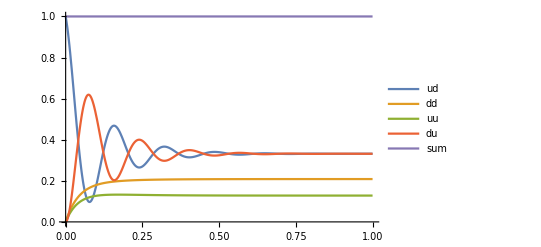

```mathematica
Plot[{Evaluate[a[2,2][t]/.solth],Evaluate[a[4,4][t]/.solth],Evaluate[a[1,1][t]/.solth],Evaluate[a[3,3][t]/.solth],Evaluate[a[3,3][t]/.solth]+Evaluate[a[4,4][t]/.solth]+Evaluate[a[1,1][t]/.solth]+Evaluate[a[2,2][t]/.solth]},{t,0,1},PlotLegends->{"ud","dd","uu","du","sum"}]
```

```mathematica
Table[{t,Evaluate[a[2,2][t]/.solsq]+Evaluate[a[4,4][t]/.solsq]+Evaluate[a[1,1][t]/.solsq]+Evaluate[a[3,3][t]/.solsq]},{t,0,1.1,0.11}]
```

```mathematica
sol=NDSolve[{ρ'[t]==-1/2((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-I Λ21(σ1p.σ2m.ρ[t]-ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m),ρ[0]==init},slnn,{t,0,10}];
```

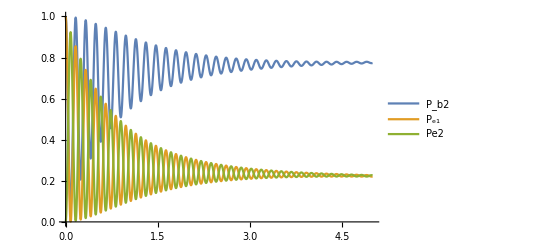

```mathematica
Plot[{Evaluate[a[2,2][t]/.sol]+Evaluate[a[4,4][t]/.sol],Evaluate[a[1,1][t]/.sol]+Evaluate[a[2,2][t]/.sol],Evaluate[a[1,1][t]/.sol]+Evaluate[a[3,3][t]/.sol]},{t,0,5},PlotRange->{0,1},PlotLegends->{"P_b2","P_e1","Pe2"}]/.sol(*b2 prob*)
```

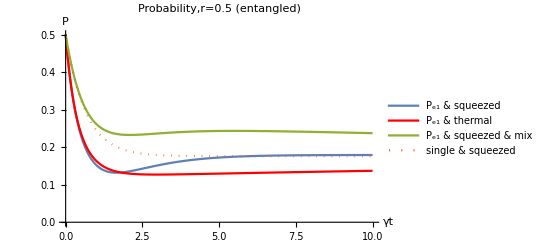

```mathematica
Plot[{Evaluate[a[1,1][t]/.solsqetg2]+Evaluate[a[2,2][t]/.solsqetg2],Evaluate[a[1,1][t]/.thetg2]+Evaluate[a[2,2][t]/.thetg2],Evaluate[a[1,1][t]/.solsqth2]+Evaluate[a[2,2][t]/.solsqth2],Evaluate[s[1,1][t]/.solsqsx]},{t,0,10},PlotLegends->{"P_e1 & squeezed","P_e1 & thermal","P_e1 & squeezed & mix","single & squeezed"},PlotRange->{{0,10},{0,0.5}},PlotStyle->{Thick,Red,,Dotted,Dashed},AxesLabel->{"γt","P"},PlotLabel->"Probability,r=0.5 (entangled)"]
```

```mathematica
Λ12
```

23.0825